```mathematica
(*The dispersion relation*)
$Assumptions->{v≥0,0≤u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
Ο=(Ν/.disp⟦1⟧)/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]}//Simplify;
X=(Ν/.disp⟦2⟧)/.{ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]}//Simplify;
Clear[a,b,c,disp]
```

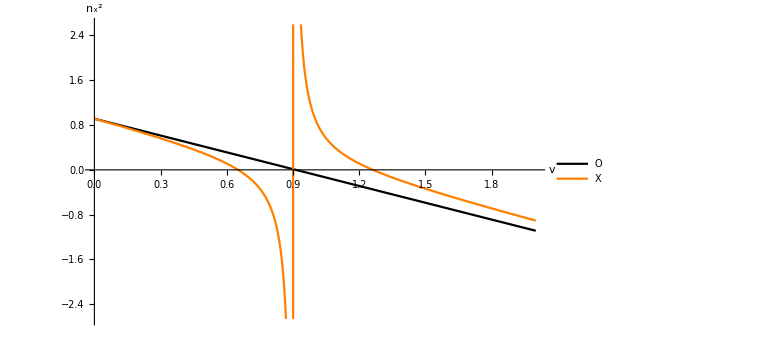

```mathematica
(*η=0*)
params={u->0.1,θ->0.3,η->0};
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,Automatic},PlotLegends->Placed[{"Ο","X"},Scaled[{0.7,0.7}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/eta.png",%,"PNG"]*)
Clear[params];
```

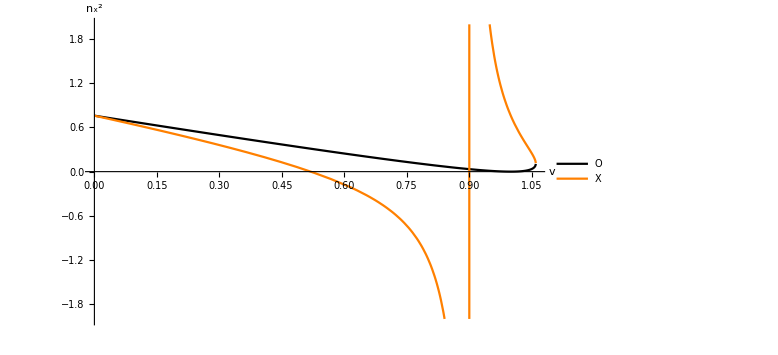

```mathematica
(*θ=0*)
params={u->υ,θ->0,η->ArcSin[√((√υ)/(1+√υ))]}/.υ->0.1;
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,{-2,2}},PlotLegends->Placed[{"Ο","X"},Scaled[{0.9,0.8}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/teta.png",%,"PNG"]*)
Clear[params];
```